```mathematica
medioDMEMF12Advanced=Import["/Users/baperez/Documents/paper/data/c_DMEM_AdvanceVALORES.txt","List"];
medioDMEMlow=Import["/Users/baperez/Documents/paper/data/medioDMEMlow_VALORES.txt","List"];

medioOPT=Import["/Users/baperez/Documents/paper/data/medioOpt01_toxicidad.txt","List"];
```

```mathematica
mets=Import["/Users/baperez/Documents/paper/data/mets_name.txt","List"];
```

```mathematica
listDMEM = {167,170,193,197,199,201,202,204,206,211,213,220,247,248,249,293,305,312,313,317,325,331,341,342,359,363,365,380,671,906,1994,2102,2514,2520,234};
listDMEMlow = {199,201,202,206,220,234,247,248,293,305,312,313,317,325,331,342,359,363,365,380,2102,2514,2520};
listOPT = {199,201,202,206,213,234,247,248,249,293,305,312,313,317,325,331,341,342,359,363,365,2102,2514,2520};
```

```mathematica
mets[[listDMEM[[Ordering[medioDMEM[[listDMEM]]]]]]]
```

{btn_e,ribflv_e,pnto_R_e,fol_e,ametam_c,thm_e,ascb_L_e,hxan_e,pydxn_e,ncam_e,inost_e,trp_L_e,asn_L_e,ala_L_e,asp_L_e,pro_L_e,glu_L_e,his_L_e,met_L_e,Lcystin_e,arg_L_e,tyr_L_e,phe_L_e,ser_L_e,gly_e,lys_L_e,thr_L_e,ile_L_e,leu_L_e,val_L_e,pi_e,gln_L_e,glc_D_e,hco3_e}

```mathematica
Ordering[medioDMEM[[listDMEM]]]
```

{12,34,24,32,30,28,8,31,33,29,20,26,3,2,10,11,15,17,22,14,7,27,9,5,13,21,6,18,19,25,23,4,16,1}

```mathematica
15
```

```mathematica
mets[[listDMEM[[{15,18,19,25,23,4,16,1}]]]]
```

{glu_L_e,ile_L_e,leu_L_e,val_L_e,pi_e,gln_L_e,glc_D_e,hco3_e}

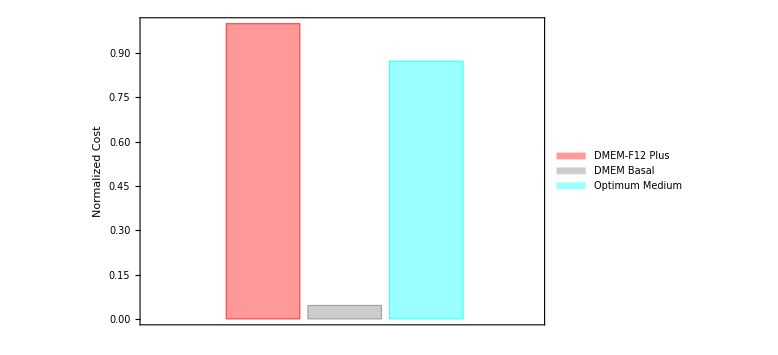

```mathematica
BarChart[{18.149279277340398/18.149279277340398,0.8308091217340441/18.149279277340398,15.845556348251993/18.149279277340398},LabelStyle->{Directive[FontSize-> 16,Black],Directive[FontSize-> 17,Black]},ImageSize->Large,ChartLegends ->Placed[{"DMEM-F12 Plus", "DMEM Basal", "Optimum Medium"},{0.6,0.93}],Frame->{{True,None},{True,None}},ChartStyle->{Directive[Red, Opacity[0.4]],Directive[Gray,Opacity[0.4]],Directive[Cyan,Opacity[0.4]],Directive[Cyan,Opacity[1]]},FrameLabel->{None,"Normalized Cost"}]
```

```mathematica
Export["/Users/baperez/Documents/Investigacion/DOCTORADO/BacthvsContinuos/BATCH_MEDIA_Optimization/new_fig/IMDM_Media_Barras.jpg",OptMediaIMDM]
```

/Users/baperez/Documents/Investigacion/DOCTORADO/BacthvsContinuos/BATCH_MEDIA_Optimization/new_fig/IMDM_Media_Barras.jpg

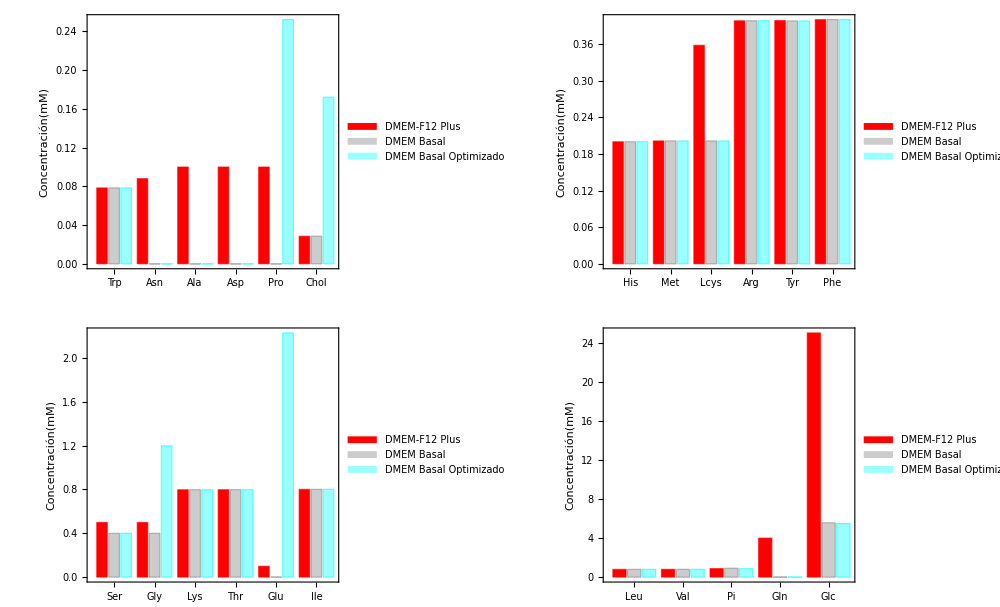

```mathematica
OptMedia=GraphicsGrid[{{BarChart[Table[{medioDMEMF12Advanced[[listDMEM]][[i]],medioDMEMlow[[listDMEM]][[i]],medioOPT[[listDMEM]][[i]]},{i,{26,3,2,10,11,35}}],LabelStyle->{Directive[FontSize-> 16,Black],Directive[FontSize-> 17,Black]},ImageSize->Large,ChartLegends ->Placed[{"DMEM-F12 Plus", "DMEM Basal", "DMEM Basal Optimizado"},{0.25,0.8}],ChartLabels->{{"Trp","Asn","Ala","Asp","Pro","Chol"},None},Frame->{{True,None},{True,None}},FrameLabel->{None,"Concentración(mM)"},ChartStyle->{Directive[Red, Opacity[1]],Directive[Gray,Opacity[0.4]],Directive[Cyan,Opacity[0.4]],Directive[Cyan,Opacity[1]]}],BarChart[Table[{medioDMEMF12Advanced[[listDMEM]][[i]],medioDMEMlow[[listDMEM]][[i]],medioOPT[[listDMEM]][[i]]},{i,{17,22,14,7,27,9}}],LabelStyle->{Directive[FontSize-> 16,Black],Directive[FontSize-> 17,Black]},ImageSize->Large,ChartLegends ->Placed[{"DMEM-F12 Plus", "DMEM Basal", "DMEM Basal Optimizado"},{0.25,0.8}],ChartLabels->{{"His","Met", "Lcys","Arg","Tyr","Phe"},None},Frame->{{True,None},{True,None}},FrameLabel->{None,"Concentración(mM)"},ChartStyle->{Directive[Red, Opacity[1]],Directive[Gray,Opacity[0.4]],Directive[Cyan,Opacity[0.4]]}]},{BarChart[Table[{medioDMEMF12Advanced[[listDMEM]][[i]],medioDMEMlow[[listDMEM]][[i]],medioOPT[[listDMEM]][[i]]},{i,{5,13,21,6,15,18}}],LabelStyle->{Directive[FontSize-> 16,Black],Directive[FontSize-> 17,Black]},ImageSize->Large,ChartLegends ->Placed[{"DMEM-F12 Plus", "DMEM Basal", "DMEM Basal Optimizado"},{0.25,0.8}],ChartLabels->{{"Ser","Gly","Lys","Thr","Glu","Ile"},None},Frame->{{True,None},{True,None}},FrameLabel->{None,"Concentración(mM)"},ChartStyle->{Directive[Red, Opacity[1]],Directive[Gray,Opacity[0.4]],Directive[Cyan,Opacity[0.4]],Directive[Cyan,Opacity[1]]}],BarChart[Table[{medioDMEMF12Advanced[[listDMEM]][[i]],medioDMEMlow[[listDMEM]][[i]],medioOPT[[listDMEM]][[i]]},{i,{19,25,23,4,16}}],LabelStyle->{Directive[FontSize-> 16,Black],Directive[FontSize-> 17,Black]},ImageSize->Large,ChartLegends ->Placed[{"DMEM-F12 Plus", "DMEM Basal", "DMEM Basal Optimizado"},{0.25,0.8}],ChartLabels->{{"Leu","Val","Pi","Gln","Glc"},None},Frame->{{True,None},{True,None}},FrameLabel->{None,"Concentración(mM)"},ChartStyle->{Directive[Red, Opacity[1]],Directive[Gray,Opacity[0.4]],Directive[Cyan,Opacity[0.4]],Directive[Cyan,Opacity[1]]}]}},ImageSize->1000]
```

```mathematica
Export["/Users/baperez/Documents/Investigacion/DOCTORADO/TESIS/PhD_Baby_PREDEFENSA/figuras/OptMedio_batch/concentracionesOptMedio2.jpg",OptMedia]
```

/Users/baperez/Documents/Investigacion/DOCTORADO/TESIS/PhD_Baby_PREDEFENSA/figuras/OptMedio_batch/concentracionesOptMedio2.jpg